```mathematica
SetDirectory[NotebookDirectory[]]
countsRaw=Import["protein_based_rec_scores_counts_combined_mst.tsv"];
Length[countsRaw]
counts=countsRaw;
counts[[All,8;;14]]=ToExpression/@ countsRaw[[All,8;;14]];
counts[[All,-1]]=Partition[ToExpression[#],2]&/@countsRaw[[All,-1]];
talliedCounts=GatherBy[counts,{#[[1]],#[[6]],#[[14]],#[[15]]}&];
Grid[Sort[{#[[1,1]],#[[1,6]],#[[1,15]],#[[1,14]],Length[#]}&/@ talliedCounts]]
```

/Users/hayssam/Documents/ISOP_0.2/tests

4408

ar | 9630 | 0%Prot,10%Docs | LSI | 60
ar | 9630 | 0%Prot,10%Docs | LSI+STRING | 60
ar | 9630 | 25%Prot,0%Docs | LSI | 90
ar | 9630 | 25%Prot,0%Docs | LSI+STRING | 90
ar | 9630 | 25%Prot,10%Docs | LSI | 60
ar | 9630 | 25%Prot,10%Docs | LSI+STRING | 60
bcell | 9630 | 25%Prot,0%Docs | LSI | 30
bcell | 9630 | 25%Prot,0%Docs | LSI+STRING | 30
egfr | 9630 | 0%Prot,10%Docs | LSI | 60
egfr | 9630 | 0%Prot,10%Docs | LSI+STRING | 60
egfr | 9630 | 25%Prot,0%Docs | LSI | 82
egfr | 9630 | 25%Prot,0%Docs | LSI+STRING | 82
egfr | 9630 | 25%Prot,10%Docs | LSI | 60
egfr | 9630 | 25%Prot,10%Docs | LSI+STRING | 60
hsa04010 | 9630 | 0%Prot,-100%Docs | LSI | 60
hsa04010 | 9630 | 0%Prot,-100%Docs | LSI+STRING | 60
hsa04010 | 9630 | 0%Prot,10%Docs | LSI | 60
hsa04010 | 9630 | 0%Prot,10%Docs | LSI+STRING | 60
hsa04010 | 9630 | -100%Prot,0%Docs | LSI | 92
hsa04010 | 9630 | -100%Prot,0%Docs | LSI+STRING | 92
hsa04010 | 9630 | -100%Prot,-100%Docs | LSI | 6
hsa04010 | 9630 | -100%Prot,-100%Docs | LSI+STRING | 6
hsa04010 | 9630 | -100%Prot,10%Docs | LSI | 60
hsa04010 | 9630 | -100%Prot,10%Docs | LSI+STRING | 60
hsa04010 | 9630 | 10%Prot,0%Docs | LSI | 60
hsa04010 | 9630 | 10%Prot,0%Docs | LSI+STRING | 60
hsa04010 | 9630 | 10%Prot,-100%Docs | LSI | 60
hsa04010 | 9630 | 10%Prot,-100%Docs | LSI+STRING | 60
hsa04010 | 9630 | 10%Prot,10%Docs | LSI | 60
hsa04010 | 9630 | 10%Prot,10%Docs | LSI+STRING | 60
hsa04012 | 9630 | 0%Prot,-100%Docs | LSI | 60
hsa04012 | 9630 | 0%Prot,-100%Docs | LSI+STRING | 60
hsa04012 | 9630 | 0%Prot,10%Docs | LSI | 60
hsa04012 | 9630 | 0%Prot,10%Docs | LSI+STRING | 60
hsa04012 | 9630 | -100%Prot,0%Docs | LSI | 91
hsa04012 | 9630 | -100%Prot,0%Docs | LSI+STRING | 91
hsa04012 | 9630 | -100%Prot,-100%Docs | LSI | 4
hsa04012 | 9630 | -100%Prot,-100%Docs | LSI+STRING | 4
hsa04012 | 9630 | -100%Prot,10%Docs | LSI | 60
hsa04012 | 9630 | -100%Prot,10%Docs | LSI+STRING | 60
hsa04012 | 9630 | 10%Prot,0%Docs | LSI | 60
hsa04012 | 9630 | 10%Prot,0%Docs | LSI+STRING | 60
hsa04012 | 9630 | 10%Prot,-100%Docs | LSI | 60
hsa04012 | 9630 | 10%Prot,-100%Docs | LSI+STRING | 60
hsa04012 | 9630 | 10%Prot,10%Docs | LSI | 60
hsa04012 | 9630 | 10%Prot,10%Docs | LSI+STRING | 60
il2 | 9630 | 0%Prot,10%Docs | LSI | 60
il2 | 9630 | 0%Prot,10%Docs | LSI+STRING | 60
il2 | 9630 | 25%Prot,0%Docs | LSI | 97
il2 | 9630 | 25%Prot,0%Docs | LSI+STRING | 97
il2 | 9630 | 25%Prot,10%Docs | LSI | 61
il2 | 9630 | 25%Prot,10%Docs | LSI+STRING | 61
tcell | 9630 | 0%Prot,10%Docs | LSI | 60
tcell | 9630 | 0%Prot,10%Docs | LSI+STRING | 60
tcell | 9630 | 25%Prot,0%Docs | LSI | 90
tcell | 9630 | 25%Prot,0%Docs | LSI+STRING | 90
tcell | 9630 | 25%Prot,10%Docs | LSI | 60
tcell | 9630 | 25%Prot,10%Docs | LSI+STRING | 60
tgfb | 9630 | 0%Prot,10%Docs | LSI | 60
tgfb | 9630 | 0%Prot,10%Docs | LSI+STRING | 60
tgfb | 9630 | 25%Prot,0%Docs | LSI | 90
tgfb | 9630 | 25%Prot,0%Docs | LSI+STRING | 90
tgfb | 9630 | 25%Prot,10%Docs | LSI | 61
tgfb | 9630 | 25%Prot,10%Docs | LSI+STRING | 61
tgfb | 9630 | 50%Prot,0%Docs | LSI | 30
tgfb | 9630 | 50%Prot,0%Docs | LSI+STRING | 30
tnf | 9630 | 0%Prot,10%Docs | LSI | 60
tnf | 9630 | 0%Prot,10%Docs | LSI+STRING | 60
tnf | 9630 | 25%Prot,0%Docs | LSI | 60
tnf | 9630 | 25%Prot,0%Docs | LSI+STRING | 60
tnf | 9630 | 25%Prot,10%Docs | LSI | 60
tnf | 9630 | 25%Prot,10%Docs | LSI+STRING | 60

## Comparing average

We group by PW, possible edges and scoring fun

```mathematica
countStyle={Black,Dashed,Dashed};
RocStyle={Black,Red,{Gray,Dashed}};
```

```mathematica
talliedCounts=GatherBy[counts,{#[[1]],#[[6]],#[[14]],#[[15]]}&];
```

```mathematica
Length[talliedCounts[[1]]]
```

6

```mathematica
Length /@ talliedCounts
```

{6,6,1,1,1,1}

Plot them all

## Individual results

```mathematica
PlotForRow[row_]:=Module[{label,realPosEdges,realPosProt,possibleProt,possibleEdges,xlimE,xlimProt,ylimE,ylimProt,neighborStr,optimalCurveEdges,optimalCurveProt,chancePickingPositiveEdge,chancePickingPositiveProt,edgesPoints,proteinPoints,edgesPointsString,proteinPointsString,tpr,fpr,roc,tprString,fprString,rocString},
label=row[[1]];
realPosEdges=row[[5]];
realPosProt=row[[4]];
possibleProt=row[[6]];
possibleEdges=row[[7]];
xlimE=row[[5]]*3;
xlimProt=row[[4]]*3;
ylimE=row[[5]]*1.5;
ylimProt=row[[4]]*1.5;
neighborStr=If[possibleProt>9000,"Whole","In neighbor"];
optimalCurveEdges={{0,0},{realPosEdges,realPosEdges},{10000,realPosEdges}};
optimalCurveProt={{0,0},{realPosProt,realPosProt},{10000,realPosProt}};
chancePickingPositiveEdge={{0,0},{xlimE,xlimE*realPosEdges/possibleEdges}};
chancePickingPositiveProt={{0,0},{xlimProt,xlimProt*realPosProt/possibleProt}};
edgesPoints=Partition[Riffle[row[[11]],row[[12]]],2];
proteinPoints=Partition[Riffle[row[[8]],row[[9]]],2];
tpr=row[[12]]/realPosEdges;
fpr=row[[13]]/possibleEdges;
roc=Partition[Riffle[fpr,tpr],2];

{label,
neighborStr,
ListLinePlot[{edgesPoints,optimalCurveEdges,chancePickingPositiveEdge},PlotRange->{{0,xlimE},{0,ylimE}},PlotStyle->countStyle],
ListLinePlot[{proteinPoints,optimalCurveProt,chancePickingPositiveProt},PlotRange->{{0,xlimProt},{0,ylimProt}},PlotStyle->countStyle],
ListLinePlot[{roc,{{0,0},{1,1}}},PlotRange->{{0,0.1},{0,1}},PlotStyle->RocStyle],ListLinePlot[{roc,{{0,0},{1,1}}},PlotRange->{{0,1},{0,1}},PlotStyle->RocStyle]
}
]
```

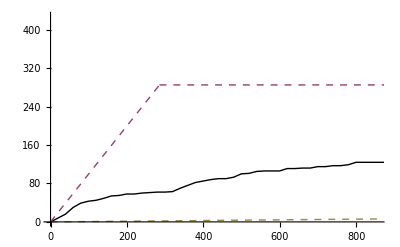
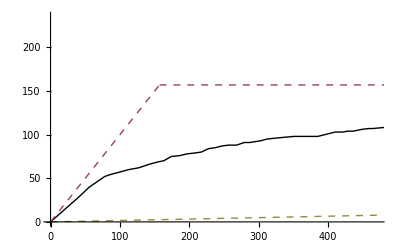
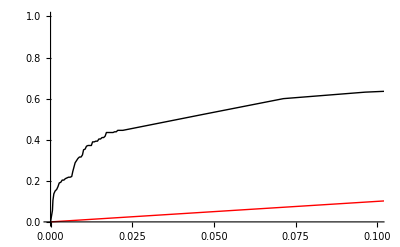
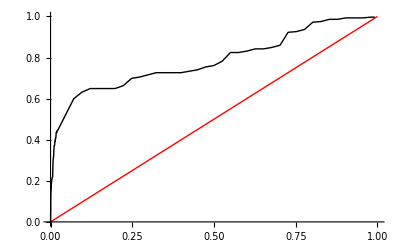
hsa04010 | Whole | -Graphics- | -Graphics- | -Graphics- | -Graphics-
hsa04010 | Whole | -Graphics- | -Graphics- | -Graphics- | -Graphics-
hsa04010 | Whole | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
PlotForRow[#]&/@talliedCounts[[1]]
]
```

## Pooled results

```mathematica
ColorData[12,"ColorList"]
```

{RGBColor[0.623529,0.145098,0.12549],RGBColor[0.658824,0.305882,0.172549],RGBColor[0.243137,0.117647,0.0588235],RGBColor[0.945098,0.752941,0.635294],RGBColor[0.839216,0.47451,0.211765],RGBColor[0.827451,0.72549,0.435294],RGBColor[0.443137,0.498039,0.54902],RGBColor[0.247059,0.309804,0.372549],RGBColor[0.168627,0.239216,0.380392],RGBColor[0.298039,0.176471,0.196078]}

```mathematica
PlotForRows[rows_,style_:{Thick,Blue}]:=Module[{label,method,realPosEdges,realPosProt,possibleProt,possibleEdges,nReps,xlimE,optTag,xlimProt,ylimE,ylimProt,neighborStr,optimalCurveProt,chancePickingPositiveEdge,chancePickingPositiveProt,edgesPoints,protsPoints,rocs,optimalCurveEdges},
label=ToUpperCase[rows[[1,1]]];
method=rows[[1,14]];
realPosEdges=rows[[1,5]];
realPosProt=rows[[1,4]];
possibleProt=rows[[1,6]];
possibleEdges=rows[[1,7]];
nReps=Length[rows];
xlimE=rows[[1,5]]*4;
optTag=rows[[1,15]];
xlimProt=rows[[1,4]]*4;
ylimE=rows[[1,5]]*1.25;
ylimProt=rows[[1,4]]*1.25;
neighborStr=If[possibleProt>9000,"HPRD",Grid[{{"Neighborhood"},{StringForm["`` prots",possibleProt]},{StringForm["`` edges",possibleEdges]}}]];optimalCurveEdges={{0,0},{realPosEdges,realPosEdges},{10000,realPosEdges}};
optimalCurveProt={{0,0},{realPosProt,realPosProt},{10000,realPosProt}};
chancePickingPositiveEdge={{0,0},{xlimE,xlimE*realPosEdges/possibleEdges}};
chancePickingPositiveProt={{0,0},{xlimProt,xlimProt*realPosProt/possibleProt}};
edgesPoints=Partition[Riffle[#[[1]],#[[2]]],2]& /@ Transpose[{rows[[All,11,2;;]],rows[[All,12,2;;]]}];
protsPoints=Partition[Riffle[#[[1]],#[[2]]],2]& /@ Transpose[{rows[[All,8,2;;]],rows[[All,9,2;;]]}];
rocs=Partition[Riffle[#[[13,2;;]]/possibleEdges,#[[12,2;;]]/realPosEdges],2]&/@ rows;
{
label,
neighborStr,
method,
optTag,
nReps,
Show[
ListLinePlot[edgesPoints,PlotRange->{{0,xlimE},{0,ylimE}},PlotStyle->style],
ListLinePlot[{optimalCurveEdges,chancePickingPositiveEdge},PlotRange->{{0,xlimE},{0,ylimE}},PlotStyle->{Dashed,Dashed}]
],
Show[
ListLinePlot[{optimalCurveProt,chancePickingPositiveProt},PlotRange->{{0,xlimProt},{0,ylimProt}},PlotStyle->{Dashed,Dashed}],
ListLinePlot[protsPoints,PlotRange->{{0,xlimProt},{0,ylimProt}},PlotStyle->style]
],
Show[
ListLinePlot[{{0,0},{1,1}},PlotRange->{{0,0.1},{0,1}},PlotStyle->Dashed],
ListLinePlot[rocs,PlotRange->{{0,0.1},{0,1}},PlotStyle->style]
],
Show[
ListLinePlot[{{0,0},{1,1}},PlotRange->{{0,1},{0,1}},PlotStyle->Dashed],
ListLinePlot[rocs,PlotRange->{{0,1},{0,1}},PlotStyle->style]
]
}
]
```

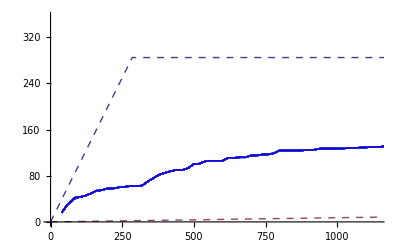
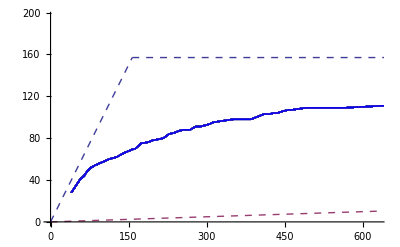
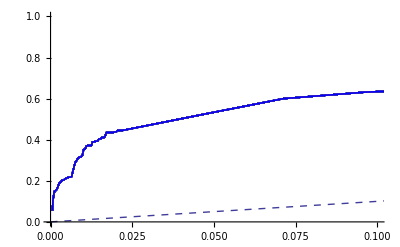
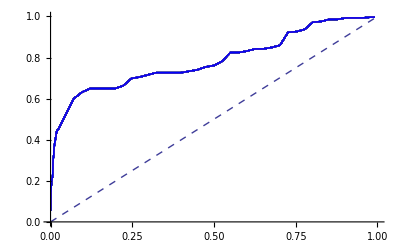
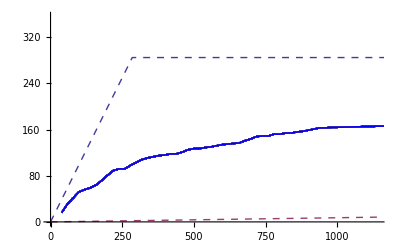
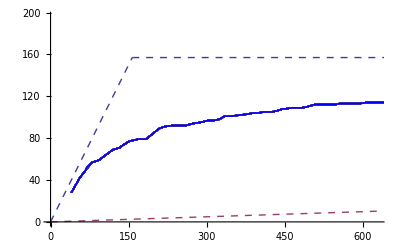
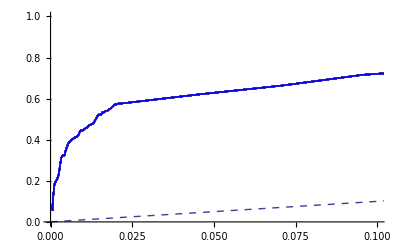
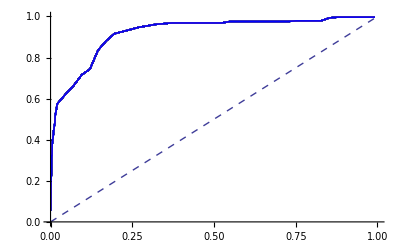
HSA04010 | HPRD | LSI | -100%Prot,0%Docs | 92 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI+STRING | -100%Prot,0%Docs | 92 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI | -100%Prot,0%Docs | 91 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | -100%Prot,0%Docs | 91 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | HPRD | LSI | 25%Prot,0%Docs | 90 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | HPRD | LSI+STRING | 25%Prot,0%Docs | 90 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI | 25%Prot,0%Docs | 90 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI+STRING | 25%Prot,0%Docs | 90 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI | 25%Prot,0%Docs | 82 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI+STRING | 25%Prot,0%Docs | 82 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TCELL | HPRD | LSI | 25%Prot,0%Docs | 90 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TCELL | HPRD | LSI+STRING | 25%Prot,0%Docs | 90 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
BCELL | HPRD | LSI | 25%Prot,0%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
BCELL | HPRD | LSI+STRING | 25%Prot,0%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | HPRD | LSI | 25%Prot,0%Docs | 97 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | HPRD | LSI+STRING | 25%Prot,0%Docs | 97 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | HPRD | LSI | 25%Prot,10%Docs | 61 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | HPRD | LSI+STRING | 25%Prot,10%Docs | 61 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | HPRD | LSI | 25%Prot,10%Docs | 61 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | HPRD | LSI+STRING | 25%Prot,10%Docs | 61 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI | -100%Prot,-100%Docs | 6 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI+STRING | -100%Prot,-100%Docs | 6 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI | 0%Prot,-100%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI+STRING | 0%Prot,-100%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI | 10%Prot,-100%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI+STRING | 10%Prot,-100%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI | 10%Prot,0%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI+STRING | 10%Prot,0%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI | -100%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI+STRING | -100%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI+STRING | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI | 10%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI+STRING | 10%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI | -100%Prot,-100%Docs | 4 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | -100%Prot,-100%Docs | 4 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI | 0%Prot,-100%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | 0%Prot,-100%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI | 10%Prot,-100%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | 10%Prot,-100%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI | 10%Prot,0%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | 10%Prot,0%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI | -100%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | -100%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI | 10%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | 10%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI+STRING | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI | 25%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI+STRING | 25%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI+STRING | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI | 25%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI+STRING | 25%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | HPRD | LSI | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | HPRD | LSI+STRING | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TNF | HPRD | LSI | 25%Prot,0%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TNF | HPRD | LSI+STRING | 25%Prot,0%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TNF | HPRD | LSI | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TNF | HPRD | LSI+STRING | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TNF | HPRD | LSI | 25%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TNF | HPRD | LSI+STRING | 25%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TCELL | HPRD | LSI | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TCELL | HPRD | LSI+STRING | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TCELL | HPRD | LSI | 25%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TCELL | HPRD | LSI+STRING | 25%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | HPRD | LSI | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | HPRD | LSI+STRING | 0%Prot,10%Docs | 60 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
PlotForRows[#]&/@talliedCounts,Frame->All
]
```

## Threshold results

```mathematica
EvalAtKnowThr[rows_]:=Module[{edgesPoints,protsPoints,edgesFs,protFs},
edgesPoints=Union[Partition[Riffle[#[[1]],#[[2]]],2]]& /@ Transpose[{rows[[All,11,2;;]],rows[[All,12,2;;]]}];
protsPoints=Union[Partition[Riffle[#[[1]],#[[2]]],2]]& /@ Transpose[{rows[[All,8,2;;]],rows[[All,9,2;;]]}];
edgesFs  = Interpolation /@ edgesPoints;
protFs  = Interpolation /@ protsPoints;
Quiet[{Table[{i,Mean[N[#[i]&/@edgesFs ]]},{i,{77,85,100,200,300,500,2000}}],
Table[{i,Mean[N[#[i]&/@protFs ]]},{i,{50,60,70,90,100,120,150,200,300}}]
}]
]
```

```mathematica
Grid[
SortBy[Transpose[Join[{Range[Length[talliedCounts]]},Transpose[{#[[1,1]],#[[1,6]],#[[1,14]],#[[1,15]],Length[#]}&/@ talliedCounts]]],{#[[2]],#[[4]],#[[3]]}&]
]
```

7 | ar | 9630 | LSI | 25%Prot,0%Docs | 90
49 | ar | 9630 | LSI | 0%Prot,10%Docs | 60
51 | ar | 9630 | LSI | 25%Prot,10%Docs | 60
8 | ar | 9630 | LSI+STRING | 25%Prot,0%Docs | 90
50 | ar | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
52 | ar | 9630 | LSI+STRING | 25%Prot,10%Docs | 60
13 | bcell | 9630 | LSI | 25%Prot,0%Docs | 30
14 | bcell | 9630 | LSI+STRING | 25%Prot,0%Docs | 30
9 | egfr | 9630 | LSI | 25%Prot,0%Docs | 82
53 | egfr | 9630 | LSI | 0%Prot,10%Docs | 60
55 | egfr | 9630 | LSI | 25%Prot,10%Docs | 60
10 | egfr | 9630 | LSI+STRING | 25%Prot,0%Docs | 82
54 | egfr | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
56 | egfr | 9630 | LSI+STRING | 25%Prot,10%Docs | 60
1 | hsa04010 | 9630 | LSI | -100%Prot,0%Docs | 92
21 | hsa04010 | 9630 | LSI | -100%Prot,-100%Docs | 6
23 | hsa04010 | 9630 | LSI | 0%Prot,-100%Docs | 60
25 | hsa04010 | 9630 | LSI | 10%Prot,-100%Docs | 60
27 | hsa04010 | 9630 | LSI | 10%Prot,0%Docs | 60
29 | hsa04010 | 9630 | LSI | -100%Prot,10%Docs | 60
31 | hsa04010 | 9630 | LSI | 0%Prot,10%Docs | 60
33 | hsa04010 | 9630 | LSI | 10%Prot,10%Docs | 60
2 | hsa04010 | 9630 | LSI+STRING | -100%Prot,0%Docs | 92
22 | hsa04010 | 9630 | LSI+STRING | -100%Prot,-100%Docs | 6
24 | hsa04010 | 9630 | LSI+STRING | 0%Prot,-100%Docs | 60
26 | hsa04010 | 9630 | LSI+STRING | 10%Prot,-100%Docs | 60
28 | hsa04010 | 9630 | LSI+STRING | 10%Prot,0%Docs | 60
30 | hsa04010 | 9630 | LSI+STRING | -100%Prot,10%Docs | 60
32 | hsa04010 | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
34 | hsa04010 | 9630 | LSI+STRING | 10%Prot,10%Docs | 60
3 | hsa04012 | 9630 | LSI | -100%Prot,0%Docs | 91
35 | hsa04012 | 9630 | LSI | -100%Prot,-100%Docs | 4
37 | hsa04012 | 9630 | LSI | 0%Prot,-100%Docs | 60
39 | hsa04012 | 9630 | LSI | 10%Prot,-100%Docs | 60
41 | hsa04012 | 9630 | LSI | 10%Prot,0%Docs | 60
43 | hsa04012 | 9630 | LSI | -100%Prot,10%Docs | 60
45 | hsa04012 | 9630 | LSI | 0%Prot,10%Docs | 60
47 | hsa04012 | 9630 | LSI | 10%Prot,10%Docs | 60
4 | hsa04012 | 9630 | LSI+STRING | -100%Prot,0%Docs | 91
36 | hsa04012 | 9630 | LSI+STRING | -100%Prot,-100%Docs | 4
38 | hsa04012 | 9630 | LSI+STRING | 0%Prot,-100%Docs | 60
40 | hsa04012 | 9630 | LSI+STRING | 10%Prot,-100%Docs | 60
42 | hsa04012 | 9630 | LSI+STRING | 10%Prot,0%Docs | 60
44 | hsa04012 | 9630 | LSI+STRING | -100%Prot,10%Docs | 60
46 | hsa04012 | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
48 | hsa04012 | 9630 | LSI+STRING | 10%Prot,10%Docs | 60
15 | il2 | 9630 | LSI | 25%Prot,0%Docs | 97
17 | il2 | 9630 | LSI | 25%Prot,10%Docs | 61
69 | il2 | 9630 | LSI | 0%Prot,10%Docs | 60
16 | il2 | 9630 | LSI+STRING | 25%Prot,0%Docs | 97
18 | il2 | 9630 | LSI+STRING | 25%Prot,10%Docs | 61
70 | il2 | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
11 | tcell | 9630 | LSI | 25%Prot,0%Docs | 90
65 | tcell | 9630 | LSI | 0%Prot,10%Docs | 60
67 | tcell | 9630 | LSI | 25%Prot,10%Docs | 60
12 | tcell | 9630 | LSI+STRING | 25%Prot,0%Docs | 90
66 | tcell | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
68 | tcell | 9630 | LSI+STRING | 25%Prot,10%Docs | 60
5 | tgfb | 9630 | LSI | 25%Prot,0%Docs | 90
19 | tgfb | 9630 | LSI | 25%Prot,10%Docs | 61
57 | tgfb | 9630 | LSI | 0%Prot,10%Docs | 60
71 | tgfb | 9630 | LSI | 50%Prot,0%Docs | 21
6 | tgfb | 9630 | LSI+STRING | 25%Prot,0%Docs | 90
20 | tgfb | 9630 | LSI+STRING | 25%Prot,10%Docs | 61
58 | tgfb | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
72 | tgfb | 9630 | LSI+STRING | 50%Prot,0%Docs | 21
59 | tnf | 9630 | LSI | 25%Prot,0%Docs | 60
61 | tnf | 9630 | LSI | 0%Prot,10%Docs | 60
63 | tnf | 9630 | LSI | 25%Prot,10%Docs | 60
60 | tnf | 9630 | LSI+STRING | 25%Prot,0%Docs | 60
62 | tnf | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
64 | tnf | 9630 | LSI+STRING | 25%Prot,10%Docs | 60

```mathematica
EvalAtKnowThr[talliedCounts[[60]]]//MatrixForm
```

({{77,41.6333},{85,45.4333},{100,51.8333},{200,90.3167},{300,115.831},{500,140.993},{2000,163.714}}
{{50,44.8705},{60,53.5828},{70,60.1365},{90,68.8859},{100,72.7215},{120,78.3319},{150,84.9568},{200,92.1158},{300,99.3751}})

```mathematica
talliedCounts[[2,-1,-1]]
```

{{0.884615,0.146497},{0.365217,0.267516},{0.7,0.178344},{0,0},{0.111111,0.112281},{0.410256,0.0561404}}

```mathematica
rows=talliedCounts[[-5]];
ListLinePlot[Partition[Riffle[#[[1]],#[[2]]],2]& /@ Transpose[{rows[[All,11,2;;50]],rows[[All,12,2;;50]]}]]
```

-Graphics-

## F-Score plot

```mathematica
{#[[1,1]],#[[1,6]],#[[1,14]],#[[1,15]],Length[#]}&/@ talliedCounts
```

{{hsa04010,9630,LSI,-100%Prot,0%Docs,92},{hsa04010,9630,LSI+STRING,-100%Prot,0%Docs,92},{hsa04012,9630,LSI,-100%Prot,0%Docs,91},{hsa04012,9630,LSI+STRING,-100%Prot,0%Docs,91},{tgfb,9630,LSI,25%Prot,0%Docs,90},{tgfb,9630,LSI+STRING,25%Prot,0%Docs,90},{ar,9630,LSI,25%Prot,0%Docs,90},{ar,9630,LSI+STRING,25%Prot,0%Docs,90},{egfr,9630,LSI,25%Prot,0%Docs,82},{egfr,9630,LSI+STRING,25%Prot,0%Docs,82},{tcell,9630,LSI,25%Prot,0%Docs,90},{tcell,9630,LSI+STRING,25%Prot,0%Docs,90},{bcell,9630,LSI,25%Prot,0%Docs,30},{bcell,9630,LSI+STRING,25%Prot,0%Docs,30},{il2,9630,LSI,25%Prot,0%Docs,97},{il2,9630,LSI+STRING,25%Prot,0%Docs,97},{il2,9630,LSI,25%Prot,10%Docs,61},{il2,9630,LSI+STRING,25%Prot,10%Docs,61},{tgfb,9630,LSI,25%Prot,10%Docs,61},{tgfb,9630,LSI+STRING,25%Prot,10%Docs,61},{hsa04010,9630,LSI,-100%Prot,-100%Docs,6},{hsa04010,9630,LSI+STRING,-100%Prot,-100%Docs,6},{hsa04010,9630,LSI,0%Prot,-100%Docs,60},{hsa04010,9630,LSI+STRING,0%Prot,-100%Docs,60},{hsa04010,9630,LSI,10%Prot,-100%Docs,60},{hsa04010,9630,LSI+STRING,10%Prot,-100%Docs,60},{hsa04010,9630,LSI,10%Prot,0%Docs,60},{hsa04010,9630,LSI+STRING,10%Prot,0%Docs,60},{hsa04010,9630,LSI,-100%Prot,10%Docs,60},{hsa04010,9630,LSI+STRING,-100%Prot,10%Docs,60},{hsa04010,9630,LSI,0%Prot,10%Docs,60},{hsa04010,9630,LSI+STRING,0%Prot,10%Docs,60},{hsa04010,9630,LSI,10%Prot,10%Docs,60},{hsa04010,9630,LSI+STRING,10%Prot,10%Docs,60},{hsa04012,9630,LSI,-100%Prot,-100%Docs,4},{hsa04012,9630,LSI+STRING,-100%Prot,-100%Docs,4},{hsa04012,9630,LSI,0%Prot,-100%Docs,60},{hsa04012,9630,LSI+STRING,0%Prot,-100%Docs,60},{hsa04012,9630,LSI,10%Prot,-100%Docs,60},{hsa04012,9630,LSI+STRING,10%Prot,-100%Docs,60},{hsa04012,9630,LSI,10%Prot,0%Docs,60},{hsa04012,9630,LSI+STRING,10%Prot,0%Docs,60},{hsa04012,9630,LSI,-100%Prot,10%Docs,60},{hsa04012,9630,LSI+STRING,-100%Prot,10%Docs,60},{hsa04012,9630,LSI,0%Prot,10%Docs,60},{hsa04012,9630,LSI+STRING,0%Prot,10%Docs,60},{hsa04012,9630,LSI,10%Prot,10%Docs,60},{hsa04012,9630,LSI+STRING,10%Prot,10%Docs,60},{ar,9630,LSI,0%Prot,10%Docs,60},{ar,9630,LSI+STRING,0%Prot,10%Docs,60},{ar,9630,LSI,25%Prot,10%Docs,60},{ar,9630,LSI+STRING,25%Prot,10%Docs,60},{egfr,9630,LSI,0%Prot,10%Docs,60},{egfr,9630,LSI+STRING,0%Prot,10%Docs,60},{egfr,9630,LSI,25%Prot,10%Docs,60},{egfr,9630,LSI+STRING,25%Prot,10%Docs,60},{tgfb,9630,LSI,0%Prot,10%Docs,60},{tgfb,9630,LSI+STRING,0%Prot,10%Docs,60},{tnf,9630,LSI,25%Prot,0%Docs,60},{tnf,9630,LSI+STRING,25%Prot,0%Docs,60},{tnf,9630,LSI,0%Prot,10%Docs,60},{tnf,9630,LSI+STRING,0%Prot,10%Docs,60},{tnf,9630,LSI,25%Prot,10%Docs,60},{tnf,9630,LSI+STRING,25%Prot,10%Docs,60},{tcell,9630,LSI,0%Prot,10%Docs,60},{tcell,9630,LSI+STRING,0%Prot,10%Docs,60},{tcell,9630,LSI,25%Prot,10%Docs,60},{tcell,9630,LSI+STRING,25%Prot,10%Docs,60},{il2,9630,LSI,0%Prot,10%Docs,60},{il2,9630,LSI+STRING,0%Prot,10%Docs,60},{tgfb,9630,LSI,50%Prot,0%Docs,21},{tgfb,9630,LSI+STRING,50%Prot,0%Docs,21}}

```mathematica
Grid[
SortBy[Transpose[Join[{Range[Length[talliedCounts]]},Transpose[{#[[1,1]],#[[1,6]],#[[1,14]],#[[1,15]],Length[#]}&/@ talliedCounts]]],{#[[2]],#[[4]],#[[3]]}&]
]
```

7 | ar | 9630 | LSI | 25%Prot,0%Docs | 90
49 | ar | 9630 | LSI | 0%Prot,10%Docs | 60
51 | ar | 9630 | LSI | 25%Prot,10%Docs | 60
8 | ar | 9630 | LSI+STRING | 25%Prot,0%Docs | 90
50 | ar | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
52 | ar | 9630 | LSI+STRING | 25%Prot,10%Docs | 60
13 | bcell | 9630 | LSI | 25%Prot,0%Docs | 30
14 | bcell | 9630 | LSI+STRING | 25%Prot,0%Docs | 30
9 | egfr | 9630 | LSI | 25%Prot,0%Docs | 82
53 | egfr | 9630 | LSI | 0%Prot,10%Docs | 60
55 | egfr | 9630 | LSI | 25%Prot,10%Docs | 60
10 | egfr | 9630 | LSI+STRING | 25%Prot,0%Docs | 82
54 | egfr | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
56 | egfr | 9630 | LSI+STRING | 25%Prot,10%Docs | 60
1 | hsa04010 | 9630 | LSI | -100%Prot,0%Docs | 92
21 | hsa04010 | 9630 | LSI | -100%Prot,-100%Docs | 6
23 | hsa04010 | 9630 | LSI | 0%Prot,-100%Docs | 60
25 | hsa04010 | 9630 | LSI | 10%Prot,-100%Docs | 60
27 | hsa04010 | 9630 | LSI | 10%Prot,0%Docs | 60
29 | hsa04010 | 9630 | LSI | -100%Prot,10%Docs | 60
31 | hsa04010 | 9630 | LSI | 0%Prot,10%Docs | 60
33 | hsa04010 | 9630 | LSI | 10%Prot,10%Docs | 60
2 | hsa04010 | 9630 | LSI+STRING | -100%Prot,0%Docs | 92
22 | hsa04010 | 9630 | LSI+STRING | -100%Prot,-100%Docs | 6
24 | hsa04010 | 9630 | LSI+STRING | 0%Prot,-100%Docs | 60
26 | hsa04010 | 9630 | LSI+STRING | 10%Prot,-100%Docs | 60
28 | hsa04010 | 9630 | LSI+STRING | 10%Prot,0%Docs | 60
30 | hsa04010 | 9630 | LSI+STRING | -100%Prot,10%Docs | 60
32 | hsa04010 | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
34 | hsa04010 | 9630 | LSI+STRING | 10%Prot,10%Docs | 60
3 | hsa04012 | 9630 | LSI | -100%Prot,0%Docs | 91
35 | hsa04012 | 9630 | LSI | -100%Prot,-100%Docs | 4
37 | hsa04012 | 9630 | LSI | 0%Prot,-100%Docs | 60
39 | hsa04012 | 9630 | LSI | 10%Prot,-100%Docs | 60
41 | hsa04012 | 9630 | LSI | 10%Prot,0%Docs | 60
43 | hsa04012 | 9630 | LSI | -100%Prot,10%Docs | 60
45 | hsa04012 | 9630 | LSI | 0%Prot,10%Docs | 60
47 | hsa04012 | 9630 | LSI | 10%Prot,10%Docs | 60
4 | hsa04012 | 9630 | LSI+STRING | -100%Prot,0%Docs | 91
36 | hsa04012 | 9630 | LSI+STRING | -100%Prot,-100%Docs | 4
38 | hsa04012 | 9630 | LSI+STRING | 0%Prot,-100%Docs | 60
40 | hsa04012 | 9630 | LSI+STRING | 10%Prot,-100%Docs | 60
42 | hsa04012 | 9630 | LSI+STRING | 10%Prot,0%Docs | 60
44 | hsa04012 | 9630 | LSI+STRING | -100%Prot,10%Docs | 60
46 | hsa04012 | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
48 | hsa04012 | 9630 | LSI+STRING | 10%Prot,10%Docs | 60
15 | il2 | 9630 | LSI | 25%Prot,0%Docs | 97
17 | il2 | 9630 | LSI | 25%Prot,10%Docs | 61
69 | il2 | 9630 | LSI | 0%Prot,10%Docs | 60
16 | il2 | 9630 | LSI+STRING | 25%Prot,0%Docs | 97
18 | il2 | 9630 | LSI+STRING | 25%Prot,10%Docs | 61
70 | il2 | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
11 | tcell | 9630 | LSI | 25%Prot,0%Docs | 90
65 | tcell | 9630 | LSI | 0%Prot,10%Docs | 60
67 | tcell | 9630 | LSI | 25%Prot,10%Docs | 60
12 | tcell | 9630 | LSI+STRING | 25%Prot,0%Docs | 90
66 | tcell | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
68 | tcell | 9630 | LSI+STRING | 25%Prot,10%Docs | 60
5 | tgfb | 9630 | LSI | 25%Prot,0%Docs | 90
19 | tgfb | 9630 | LSI | 25%Prot,10%Docs | 61
57 | tgfb | 9630 | LSI | 0%Prot,10%Docs | 60
71 | tgfb | 9630 | LSI | 50%Prot,0%Docs | 21
6 | tgfb | 9630 | LSI+STRING | 25%Prot,0%Docs | 90
20 | tgfb | 9630 | LSI+STRING | 25%Prot,10%Docs | 61
58 | tgfb | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
72 | tgfb | 9630 | LSI+STRING | 50%Prot,0%Docs | 21
59 | tnf | 9630 | LSI | 25%Prot,0%Docs | 60
61 | tnf | 9630 | LSI | 0%Prot,10%Docs | 60
63 | tnf | 9630 | LSI | 25%Prot,10%Docs | 60
60 | tnf | 9630 | LSI+STRING | 25%Prot,0%Docs | 60
62 | tnf | 9630 | LSI+STRING | 0%Prot,10%Docs | 60
64 | tnf | 9630 | LSI+STRING | 25%Prot,10%Docs | 60

```mathematica
FScore[prec_,rec_]:=(2*prec*rec)/(prec+rec)
```

```mathematica
rows=talliedCounts[[56,-1;;-1,All]];
```

```mathematica
realPosEdges=rows[[1,5]];
realPosProt=rows[[1,4]];
precE=N[rows[[1,12,2;;]]/rows[[1,11,2;;]]];
recE=N[rows[[1,12,2;;]]/realPosEdges];
PRPointsE=Partition[Riffle[recE,precE],2];
precP=N[rows[[1,9,2;;]]/rows[[1,8,2;;]]];
recP=N[rows[[1,9,2;;]]/realPosProt];
PRPointsP=Partition[Riffle[recP,precP],2];

protPrior=Reverse/@rows[[1,16,;;3]]
edgesPrior=Reverse/@rows[[1,16,4;;]]
```

{{0.244755,1.},{0.475524,0.561983},{0.27972,0.97561}}

{{0,0},{0.367857,0.285319},{0.0964286,0.675}}

```mathematica
btie04012E={{0.12,0.21},{0.05,0.29}};
btie04012P={{0.35,0.45},{0.23,0.77}};
btie04010E={{0.10,0.33},{0.06,0.44}};
btie04010P={{0.25,0.57},{0.22,0.74}};
```

```mathematica
Show[{
ListLinePlot[PRPointsE,PlotRange->{{0,1},{0,1}}],
Graph[{"Prior"->"Sho","Sho"->"MST"},VertexCoordinates->edgesPrior],
Graphics[Point[btie04012E]]
}]
```

-Graphics-

```mathematica
Show[{
ListLinePlot[PRPointsP,PlotRange->{{0,1},{0,1}}],
Graph[{"Prior"->"Sho","Sho"->"MST"},VertexCoordinates->protPrior],
Graphics[Point[btie04012P]]
}]
```

-Graphics-

```mathematica
l={
{"hsa04010",9630,LSI,"-100%Prot,0%Docs",92},{"hsa04010",9630,LSI+STRING,"-100%Prot,0%Docs",92},{"hsa04012",9630,LSI,"-100%Prot,0%Docs",91},{"hsa04012",9630,LSI+STRING,"-100%Prot,0%Docs",91},{"tgfb",9630,LSI,"25%Prot,0%Docs",90},{"tgfb",9630,LSI+STRING,"25%Prot,0%Docs",90},{"ar",9630,LSI,"25%Prot,0%Docs",90},{"ar",9630,LSI+STRING,"25%Prot,0%Docs",90},{"egfr",9630,LSI,"25%Prot,0%Docs",82},{"egfr",9630,LSI+STRING,"25%Prot,0%Docs",82},{"tcell",9630,LSI,"25%Prot,0%Docs",90},{"tcell",9630,LSI+STRING,"25%Prot,0%Docs",90},{"bcell",9630,LSI,"25%Prot,0%Docs",30},{"bcell",9630,LSI+STRING,"25%Prot,0%Docs",30},{"il2",9630,LSI,"25%Prot,0%Docs",97},{"il2",9630,LSI+STRING,"25%Prot,0%Docs",97},{"il2",9630,LSI,"25%Prot,10%Docs",61},{"il2",9630,LSI+STRING,"25%Prot,10%Docs",61},{"tgfb",9630,LSI,"25%Prot,10%Docs",61}
}
```

{{hsa04010,9630,LSI,-100%Prot,0%Docs,92},{hsa04010,9630,LSI+STRING,-100%Prot,0%Docs,92},{hsa04012,9630,LSI,-100%Prot,0%Docs,91},{hsa04012,9630,LSI+STRING,-100%Prot,0%Docs,91},{tgfb,9630,LSI,25%Prot,0%Docs,90},{tgfb,9630,LSI+STRING,25%Prot,0%Docs,90},{ar,9630,LSI,25%Prot,0%Docs,90},{ar,9630,LSI+STRING,25%Prot,0%Docs,90},{egfr,9630,LSI,25%Prot,0%Docs,82},{egfr,9630,LSI+STRING,25%Prot,0%Docs,82},{tcell,9630,LSI,25%Prot,0%Docs,90},{tcell,9630,LSI+STRING,25%Prot,0%Docs,90},{bcell,9630,LSI,25%Prot,0%Docs,30},{bcell,9630,LSI+STRING,25%Prot,0%Docs,30},{il2,9630,LSI,25%Prot,0%Docs,97},{il2,9630,LSI+STRING,25%Prot,0%Docs,97},{il2,9630,LSI,25%Prot,10%Docs,61},{il2,9630,LSI+STRING,25%Prot,10%Docs,61},{tgfb,9630,LSI,25%Prot,10%Docs,61}}

```mathematica
Dimensions[l]
```

{19,5}

```mathematica
lp=Transpose[Join[{Range[Length[l]]},Transpose[l]]]
Dimensions[lp]
Grid[lp]
```

{{1,hsa04010,9630,LSI,-100%Prot,0%Docs,92},{2,hsa04010,9630,LSI+STRING,-100%Prot,0%Docs,92},{3,hsa04012,9630,LSI,-100%Prot,0%Docs,91},{4,hsa04012,9630,LSI+STRING,-100%Prot,0%Docs,91},{5,tgfb,9630,LSI,25%Prot,0%Docs,90},{6,tgfb,9630,LSI+STRING,25%Prot,0%Docs,90},{7,ar,9630,LSI,25%Prot,0%Docs,90},{8,ar,9630,LSI+STRING,25%Prot,0%Docs,90},{9,egfr,9630,LSI,25%Prot,0%Docs,82},{10,egfr,9630,LSI+STRING,25%Prot,0%Docs,82},{11,tcell,9630,LSI,25%Prot,0%Docs,90},{12,tcell,9630,LSI+STRING,25%Prot,0%Docs,90},{13,bcell,9630,LSI,25%Prot,0%Docs,30},{14,bcell,9630,LSI+STRING,25%Prot,0%Docs,30},{15,il2,9630,LSI,25%Prot,0%Docs,97},{16,il2,9630,LSI+STRING,25%Prot,0%Docs,97},{17,il2,9630,LSI,25%Prot,10%Docs,61},{18,il2,9630,LSI+STRING,25%Prot,10%Docs,61},{19,tgfb,9630,LSI,25%Prot,10%Docs,61}}

{19,6}

1 | hsa04010 | 9630 | LSI | -100%Prot,0%Docs | 92
2 | hsa04010 | 9630 | LSI+STRING | -100%Prot,0%Docs | 92
3 | hsa04012 | 9630 | LSI | -100%Prot,0%Docs | 91
4 | hsa04012 | 9630 | LSI+STRING | -100%Prot,0%Docs | 91
5 | tgfb | 9630 | LSI | 25%Prot,0%Docs | 90
6 | tgfb | 9630 | LSI+STRING | 25%Prot,0%Docs | 90
7 | ar | 9630 | LSI | 25%Prot,0%Docs | 90
8 | ar | 9630 | LSI+STRING | 25%Prot,0%Docs | 90
9 | egfr | 9630 | LSI | 25%Prot,0%Docs | 82
10 | egfr | 9630 | LSI+STRING | 25%Prot,0%Docs | 82
11 | tcell | 9630 | LSI | 25%Prot,0%Docs | 90
12 | tcell | 9630 | LSI+STRING | 25%Prot,0%Docs | 90
13 | bcell | 9630 | LSI | 25%Prot,0%Docs | 30
14 | bcell | 9630 | LSI+STRING | 25%Prot,0%Docs | 30
15 | il2 | 9630 | LSI | 25%Prot,0%Docs | 97
16 | il2 | 9630 | LSI+STRING | 25%Prot,0%Docs | 97
17 | il2 | 9630 | LSI | 25%Prot,10%Docs | 61
18 | il2 | 9630 | LSI+STRING | 25%Prot,10%Docs | 61
19 | tgfb | 9630 | LSI | 25%Prot,10%Docs | 61

Transpose::nmtx: The first two levels of the one-dimensional list {{1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19}, {"hsa04010", 9630, LSI, "-100%Prot,0%Docs", 92}, {"hsa04010", 9630, LSI + STRING, "-100%Prot,0%Docs", 92}, {"hsa04012", 9630, LSI, "-100%Prot,0%Docs", 91}, {"hsa04012", 9630, LSI + STRING, "-100%Prot,0%Docs", 91}, {"tgfb", 9630, LSI, "25%Prot,0%Docs", 90}, {"tgfb", 9630, LSI + STRING, "25%Prot,0%Docs", 90}, {"ar", 9630, LSI, "25%Prot,0%Docs", 90}, « 5 », {"bcell", 9630, LSI, "25%Prot,0%Docs", 30}, {"bcell", 9630, LSI + STRING, "25%Prot,0%Docs", 30}, {"il2", 9630, LSI, "25%Prot,0%Docs", 97}, {"il2", 9630, LSI + STRING, "25%Prot,0%Docs", 97}, {"il2", 9630, LSI, "25%Prot,10%Docs", 61}, {"il2", 9630, LSI + STRING, "25%Prot,10%Docs", 61}, {"tgfb", 9630, LSI, "25%Prot,10%Docs", 61}} cannot be transposed.

Grid[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},{hsa04010,9630,LSI,-100%Prot,0%Docs,92},{hsa04010,9630,LSI+STRING,-100%Prot,0%Docs,92},{hsa04012,9630,LSI,-100%Prot,0%Docs,91},{hsa04012,9630,LSI+STRING,-100%Prot,0%Docs,91},{tgfb,9630,LSI,25%Prot,0%Docs,90},{tgfb,9630,LSI+STRING,25%Prot,0%Docs,90},{ar,9630,LSI,25%Prot,0%Docs,90},{ar,9630,LSI+STRING,25%Prot,0%Docs,90},{egfr,9630,LSI,25%Prot,0%Docs,82},{egfr,9630,LSI+STRING,25%Prot,0%Docs,82},{tcell,9630,LSI,25%Prot,0%Docs,90},{tcell,9630,LSI+STRING,25%Prot,0%Docs,90},{bcell,9630,LSI,25%Prot,0%Docs,30},{bcell,9630,LSI+STRING,25%Prot,0%Docs,30},{il2,9630,LSI,25%Prot,0%Docs,97},{il2,9630,LSI+STRING,25%Prot,0%Docs,97},{il2,9630,LSI,25%Prot,10%Docs,61},{il2,9630,LSI+STRING,25%Prot,10%Docs,61},{tgfb,9630,LSI,25%Prot,10%Docs,61}}]]